# Spin channels - state-vector engine

## Definitions

## 0 - Session setup

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
LaunchKernels[12];
```

```mathematica
Get["C:\\Users\\Miguel\\Github\\libs\\QMB\\Kernel\\init.m"];
```

```mathematica
Names["QMB`*"]
```

{AnalyticalNumberVarianceGOE,AnalyticalNumberVarianceGUE,AnalyticalNumberVariancePoisson,ARQMHamiltonian,BlochVector,BoseHubbardHamiltonian,BoseHubbardHilbertSpaceDimension,BosonEscapeKrausOperators,BosonicPartialTrace,Braket,ClassicalMapeo,ClassicalStep,ClassicalToDisk,ClassicalToSphere,COEAsymptoticSigma2,COESFFAnalytical,coherentstate,CommutationQ,CompileLevelCounter,CompileSFF,ComplexSpacingRatios,ComplexToPolar,ComputeSigma2Sliding,Concurrence,DensityMatrix,Dyad,EigenvectorQ,EmpiricalKLDivergence,EnsembleSFF,EnsembleSigma2,EvaluateSpectrumSigma2,FixCkForStateEvoultion,Floq,Floqb,Floqbn,Floqn,Floqsym,FluctuationPowerSpectrum,FockBasis,FockBasisIndex,FockBasisStateAsColumnVector,FuzzyMeasurement,FuzzyMeasurementChannel,GenerateCOEEnsemble,generateCoherentStateCompiler,GenerateGinibreMatrix,GenerateQKTEnsemble,generateSpinOperators,GetFluctuations,GetQKTParityEigensystem,GetQKTParitySpectra,HaarRandomState,HilbertSpaceDim,InitializationBosonicPartialTrace,InitializeVariables,IntWignerCOE,IPR,KetInComputationalBasisFromVector,KineticTermBoseHubbardHamiltonian,KLDivergence,KroneckerVectorProduct,kthOrderSpacings,LengthSpectrum,LevelSpacingDistribution,MatrixCommutator,MatrixPartialTrace,MatrixPartialTraceFromPureState,MeanLevelSpacingRatio,MutuallyCommutingSetQ,NNSpacings,NormalizedSpacingRatios,NumberVariance,ParitySectorIndices,PartialTranspose,Pauli,PoolSpacingRatios,PoolSpacings,PotentialTermBoseHubbardHamiltonian,PrCOE,PrCUE,PrPoisson,Purity,QuantumTexture,Qubit,QubitStateFromBlochVector,RandomChainProductState,RandomCOESpectrum,RandomQubitState,RandomSU2Parameters,RandomSU2Rotation,RatiosDistribution,RatiosDistributionPoisson,RenyiEntropy,Reshuffle,SingleSFF,SingleSpectrumSigma2,SortFockBasis,SpacingRatios,SpectralFormFactor,SpectralFormFactorRMT,StateEvolution,SU2Rotation,SU2RotationParameters,SuperoperatorFromU,SwapMatrix,SymmetricSubspace,Tag,TimeAveragedSFF,Unfold,UnfoldLinear,ValidateUnfolding,VectorFromKetInComputationalBasis,WeylMatrix,WignerCOE,ω}

```mathematica
?ValidateUnfolding
```

```mathematica
?Unfold
```

```mathematica
(* Compile target for this session. Falls back to "WVM" if no C compiler. *)
$CompileTarget = "C";
```

## 1 - Compiled partial traces (4x4 rhoAB, layout (q1,q2))

```mathematica
Clear[TraceOutA, TraceOutB];
TraceOutB = Compile[                  (* keep spin A, trace out B *)
  {{ρ, _Complex, 2}},
  {{ρ[[1,1]] + ρ[[2,2]],  ρ[[1,3]] + ρ[[2,4]]},
   {ρ[[3,1]] + ρ[[4,2]],  ρ[[3,3]] + ρ[[4,4]]}},
  CompilationTarget -> $CompileTarget, RuntimeOptions -> "Speed"
];
TraceOutA = Compile[                  (* keep spin B, trace out A *)
  {{ρ, _Complex, 2}},
  {{ρ[[1,1]] + ρ[[3,3]],  ρ[[1,2]] + ρ[[3,4]]},
   {ρ[[2,1]] + ρ[[4,3]],  ρ[[2,2]] + ρ[[4,4]]}},
  CompilationTarget -> $CompileTarget, RuntimeOptions -> "Speed"
];
```

## 2 - Von Neumann entropy

```mathematica
Clear[VNEntropy2x2, VNEntropy4x4];
VNEntropy2x2 = Compile[
  {{ρ, _Complex, 2}},
  Module[{r11, r22, r12r, r12i, absq, disc, λ1, λ2},
    r11  = Re[ρ[[1,1]]]; r22 = Re[ρ[[2,2]]];
    r12r = Re[ρ[[1,2]]]; r12i = Im[ρ[[1,2]]];
    absq = r12r^2 + r12i^2;
    disc = Sqrt[(r11 - r22)^2 + 4.*absq];
    λ1 = (r11 + r22 + disc)/2.; λ2 = (r11 + r22 - disc)/2.;
    If[λ1 > 1.*^-14, -λ1*Log[λ1], 0.] +
    If[λ2 > 1.*^-14, -λ2*Log[λ2], 0.]
  ],
  CompilationTarget -> $CompileTarget, RuntimeOptions -> "Speed"
];
VNEntropy4x4[ρ_] := Module[
  {λ = Select[Re[Eigenvalues[N[ρ]]], # > 1.*^-14 &]},
  -λ . Log[λ]
];
```

## 3 - Concurrence (Wootters 1998)

```mathematica
spinFlip = N[KroneckerProduct[PauliMatrix[2], PauliMatrix[2]]];
Clear[Concurrence];
Concurrence[ρ_] := Module[
  {ρTilde, λs},
  ρTilde = spinFlip . Conjugate[ρ] . spinFlip;
  λs = Reverse[Sort[Re[Sqrt[Chop[Eigenvalues[ρ . ρTilde]]]]]];
  Max[0., λs[[1]] - λs[[2]] - λs[[3]] - λs[[4]]]
];
```

## 4 - Single-pass observable aggregator

```mathematica
Clear[ComputeAllObservables];
ComputeAllObservables[ρAB_, ρref_] := Module[
  {ρA, ρB, SA, SB, SAB},
  ρA = TraceOutB[ρAB]; ρB = TraceOutA[ρAB];
  SA = VNEntropy2x2[ρA]; SB = VNEntropy2x2[ρB];
  SAB = VNEntropy4x4[ρAB];
  <|
    "Concurrence"  -> Concurrence[ρAB],
    "Purity"       -> Re[Tr[ρAB . ρAB]],
    "EntropyA"     -> SA,
    "EntropyB"     -> SB,
    "MutualInfo"   -> SA + SB - SAB,
    "SpinSurvival" -> Re[Tr[ρref . ρAB]]   (* overlap with reference; a fidelity only if ρref is pure *)
  |>
];
```

## 5 - Pauli operators

```mathematica
σx = N[PauliMatrix[1]]; σy = N[PauliMatrix[2]]; σz = N[PauliMatrix[3]];
σp = σx + I*σy;   (* raising:  {{0,2},{0,0}} *)
σm = σx - I*σy;   (* lowering: {{0,0},{2,0}} *)
id2 = N[IdentityMatrix[2]];
```

## 6 - Hamiltonian embeddings and boundary couplings

```mathematica
Clear[SparseId, EmbedSpinA, EmbedSpinB, EmbedChain, EmbedChainSite];
SparseId[n_] := SparseArray[Band[{1, 1}] -> 1., {n, n}];
EmbedSpinA[op_, L_]      := KroneckerProduct[op, SparseId[2^L], SparseId[2]];
EmbedSpinB[op_, L_]      := KroneckerProduct[SparseId[2], SparseId[2^L], op];
EmbedChain[Ha_, L_]      := KroneckerProduct[SparseId[2], Ha, SparseId[2]];
EmbedChainSite[op_, k_, L_] := KroneckerProduct[SparseId[2^(k-1)], op, SparseId[2^(L-k)]];

Clear[BuildCouplingAChain, BuildCouplingBChain, BuildFullHamiltonian];
(* A couples to the FIRST chain site; B to the LAST. *)
BuildCouplingAChain[couplingTerms_, L_] := Sum[
  term[[1]] * KroneckerProduct[term[[2]], KroneckerProduct[term[[3]], SparseId[2^(L-1)]], SparseId[2]],
  {term, couplingTerms}];
BuildCouplingBChain[couplingTerms_, L_] := Sum[
  term[[1]] * KroneckerProduct[SparseId[2], KroneckerProduct[SparseId[2^(L-1)], term[[2]]], term[[3]]],
  {term, couplingTerms}];
BuildFullHamiltonian[HAlocal_, Ha_, HBlocal_, couplingA_, couplingB_, L_] :=
  EmbedSpinA[HAlocal, L] + EmbedChain[Ha, L] + EmbedSpinB[HBlocal, L] +
  BuildCouplingAChain[couplingA, L] + BuildCouplingBChain[couplingB, L];
```

## 7 - Chain Hamiltonian (self-contained; matches XXZwLocalDefectHamiltonian)

```mathematica
(* Open XXZ chain with uniform field w and local defect field ed on site d:      *)
(*   H = Sum_k (1/4)[ Jxy(XX+YY) + Jz ZZ ]  +  (1/2)( w Sum_k Zk + ed Z_d ).       *)
(* Anisotropy is the Jz slot. Prefer the QMB library version if it is loaded.       *)
Clear[XXZChainSparse];
XXZChainSparse[Jxy_, Jz_, w_, ed_, L_, d_] := Module[
  {dim = 2^L, H, embNN, emb},
  emb[op_, k_]        := KroneckerProduct[SparseId[2^(k-1)], op, SparseId[2^(L-k)]];
  embNN[oa_, ob_, k_] := KroneckerProduct[SparseId[2^(k-1)], oa, ob, SparseId[2^(L-k-1)]];
  H = SparseArray[{}, {dim, dim}];
  Do[H += (1/4)*(Jxy*(embNN[σx, σx, k] + embNN[σy, σy, k]) + Jz*embNN[σz, σz, k]),
     {k, 1, L-1}];
  If[w  != 0., Do[H += (1/2)*w*emb[σz, k], {k, 1, L}]];
  If[ed != 0., H += (1/2)*ed*emb[σz, d]];
  H
];
```

## 8 - Diagonalization (real-symmetric aware)

```mathematica
(* If H is real symmetric (guard passes) the real eigensolver is used: real       *)
(* eigenvectors, ~half the memory and time of the complex path. Eigenvectors are   *)
(* returned as ROWS, sorted by ascending energy.                                   *)
Clear[DiagonalizeH];
DiagonalizeH::cmplx = "Hamiltonian has imaginary part up to `1`; complex eigensolver used.";
DiagonalizeH[HT_] := Module[
  {HN = N[HT], im, vals, vecs, ord},
  im = Max[Abs[Im[If[Head[HN] === SparseArray, HN["NonzeroValues"], Flatten[HN]]]]];
  If[im > 1.*^-12,
    Message[DiagonalizeH::cmplx, im]; HN = Normal[HN],
    HN = Re[Normal[HN]]
  ];
  {vals, vecs} = Eigensystem[HN];
  ord = Ordering[vals];
  {vals[[ord]], vecs[[ord]]}
];
```

## 9 - Wavefunction utilities

```mathematica
Clear[BuildInitialStateVector, GetRhoAB];
(* psiAB: length-4 (q1,q2);  psiChain: length-2^L.  Output layout: (q1, c, q2).    *)
BuildInitialStateVector[psiAB_List, psiChain_List, L_] := Module[{tensor},
  tensor = TensorProduct[ArrayReshape[psiAB, {2, 2}], psiChain];  (* (q1,q2,c) *)
  Flatten[Transpose[tensor, {1, 3, 2}]]                           (* (q1,c,q2) *)
];
(* Exact pure-state partial trace of the boundary spins from a (q1,c,q2) vector.    *)
GetRhoAB[psi_, L_] := Module[{M},
  M = ArrayReshape[Transpose[ArrayReshape[psi, {2, 2^L, 2}], {1, 3, 2}], {4, 2^L}];
  M . ConjugateTranspose[M]
];
```

## 10 - Thermal / ensemble state (defined here for testing)

```mathematica
(* Chain state enters only as a list of {weight, eigenvector}. This keeps the      *)
(* engine agnostic to how the mixture was produced (thermal, ground, product...).  *)
Clear[ThermalWeights, ThermalChainStates, ThermalChainDensity];

(* beta == 0        -> maximally mixed (uniform weights)                            *)
(* beta == Infinity -> equal-weight ground multiplet (degeneracy-safe)             *)
(* else             -> Boltzmann weights, shifted by ground energy for stability    *)
ThermalWeights[valsChain_, beta_] := Module[{v0, w, tol},
  Which[
    beta == 0.,
      ConstantArray[1./Length[valsChain], Length[valsChain]],
    beta === Infinity,
      v0 = Min[valsChain]; tol = 1.*^-10 Max[1., Abs[v0]];
      w = Boole[(valsChain - v0) <= tol]; w/Total[w],
    True,
      v0 = Min[valsChain]; w = Exp[-beta (valsChain - v0)]; w/Total[w]
  ]
];

(* vecsChain: rows = eigenvectors (as returned by DiagonalizeH). thr = 0. is exact; *)
(* thr > 0 drops low-weight states (an approximation; retained weights not renorm). *)
ThermalChainStates[valsChain_, vecsChain_, beta_, thr_:0.] := Module[{w},
  w = ThermalWeights[valsChain, beta];
  Select[MapThread[{#1, #2} &, {w, vecsChain}], First[#] > thr &]
];

(* Full chain density matrix, for validation against MatrixExp[-beta Ha]/Tr.       *)
ThermalChainDensity[valsChain_, vecsChain_, beta_] := Module[{w = ThermalWeights[valsChain, beta]},
  Transpose[vecsChain] . (w vecsChain)
];
```

```mathematica
(* Unravel rhoAB0 (x) rho_chain into sqrt(p)-weighted pure columns in the ENERGY   *)
(* basis. rhoAB0 may be mixed; chainStates = list of {weight, chainVector}.         *)
(* Returns PsiE0Mat : (2^(L+2)) x Nstates, ready for the evolution engine.          *)
Clear[BuildEnsembleColumns];
BuildEnsembleColumns[rhoAB0_, chainStates_, Evec_, L_] := Module[
  {vAB, UAB, cols},
  {vAB, UAB} = Eigensystem[N[rhoAB0]];        (* rows = eigenvectors *)
  cols = Reap[
    Do[
      Do[
        If[Re[vAB[[m]]] > 1.*^-12,
          Sow[ Sqrt[Re[vAB[[m]]] cs[[1]]] *
               (Evec . BuildInitialStateVector[UAB[[m]], cs[[2]], L]) ]
        ],
        {m, Length[vAB]}
      ],
      {cs, chainStates}
    ]
  ][[2]];
  cols = If[cols === {}, {}, cols[[1]]];
  Transpose[cols]
];
```

## 11 - Evolution engine (single kernel, batched BLAS)

```mathematica
(* One engine for pure and mixed states. NO subkernels / DistributeDefinitions:    *)
(* the per-step cost is a dense D x (Ns*chunk) product handled by threaded BLAS on   *)
(* the master kernel. Distributing Evec (~2 GB at L=12) across kernels was the RAM   *)
(* multiplier in the old pipeline and is avoided here.                              *)
(*                                                                                  *)
(* Global survival Tr[rho(0) rho(t)]:                                               *)
(*   Ns == 1 : rank-1 form |probE . phase|^2  (no D x D object).                     *)
(*   Ns  > 1 : quadratic form Re[phase^* . (|rhoE0|^2 . phase)], |rhoE0|^2 built once.*)
Clear[EvolveEnsemble];
Options[EvolveEnsemble] = {"MaxColumns" -> 2048};
EvolveEnsemble[Eval_, Udag_, PsiE0Mat_, rhoABref_, L_, tlist_, OptionsPattern[]] := Module[
  {Ns, Dtot, dC, maxCols, chunk, tchunks, rank1, probE, absR2},
  Ns = Dimensions[PsiE0Mat][[2]];
  Dtot = Length[Eval]; dC = 2^L;
  maxCols = OptionValue["MaxColumns"];
  rank1 = (Ns == 1);
  If[rank1,
    probE = Abs[Flatten[PsiE0Mat]]^2,
    absR2 = Abs[PsiE0Mat . ConjugateTranspose[PsiE0Mat]]^2
  ];
  chunk = Max[1, Quotient[maxCols, Ns]];
  tchunks = Partition[tlist, UpTo[chunk]];
  Reap[
    Do[
      Module[{tc, c, phase, B, PsiBig},
        tc = tchunks[[ci]]; c = Length[tc];
        phase = Exp[(-I) Outer[Times, Eval, tc]];                       (* Dtot x c *)
        B = ArrayReshape[
              Transpose[Table[phase[[All, τ]] PsiE0Mat, {τ, c}], {2, 1, 3}],
              {Dtot, c Ns}];                                            (* time-major *)
        PsiBig = Udag . B;                                             (* position basis *)
        Do[
          Module[{cols, M, rhoAB, ph, survG, obs},
            cols = PsiBig[[All, (τ-1) Ns + 1 ;; τ Ns]];
            M = ArrayReshape[
                  Transpose[ArrayReshape[cols, {2, dC, 2, Ns}], {1, 3, 2, 4}],
                  {4, dC Ns}];
            rhoAB = M . ConjugateTranspose[M];
            ph = phase[[All, τ]];
            survG = If[rank1, Abs[probE . ph]^2, Re[Conjugate[ph] . (absR2 . ph)]];
            obs = ComputeAllObservables[rhoAB, rhoABref];
            Sow[Join[<|"Time" -> tc[[τ]], "SurvivalGlobal" -> survG|>, obs]]
          ],
          {τ, c}
        ]
      ],
      {ci, Length[tchunks]}
    ]
  ][[2, 1]]
];
```

## Notes (extension points)

## Parameters

```mathematica
(* ===============  MODEL + STATE  (single editable block)  =============== *)
(* --- System size and fields --- *)
L = 12;
{Δa, Δb, λa, λb} = {1., 1., 0.1, 0.1};
HAlocal = Δa σz;
HBlocal = Δb σz;
(* Flip-flop boundary coupling. NOTE: with σp=σx+Iσy the effective XX+YY strength is 2λ. *)
couplingA = {{λa, σp, σm}, {λa, σm, σp}};
couplingB = {{λb, σp, σm}, {λb, σm, σp}};

(* --- Chain (anisotropy in the Jz slot) --- *)
{Jxy, Jz, w, ed, d} = {-1., 0.5, 0., 0., L};
```

## Method

```mathematica
L = 12;
```

```mathematica
(* ================================================================ *)
(* MODULE: U(1) Symmetry Operator (Total Magnetization Z)           *)
(* ================================================================ *)
ClearAll[BuildTotalSz];
BuildTotalSz[L_Integer] := Module[{dim, diag, state, szSum},
  dim = 2^(L + 2);
  
  (* Total Sz is a purely diagonal operator in the computational basis *)
  diag = Table[
    state = dim - row;
    (* Sum (2*Bit - 1) over all L+2 bits *)
    szSum = Sum[2 * BitGet[state, i] - 1, {i, 0, L + 1}];
    szSum,
    {row, 1, dim}
  ];
  
  SparseArray[Band[{1, 1}] -> diag, {dim, dim}]
];

(* ================================================================ *)
(* MODULE: Z2 Reflection (Parity) Operator                          *)
(* ================================================================ *)
ClearAll[BuildParity];
BuildParity[L_Integer] := Module[{dim, rules, state, revState, col},
  dim = 2^(L + 2);
  
  (* Parity is a permutation operator (off-diagonal elements of 1) *)
  rules = Table[
    state = dim - row;
    
    (* Extract the L+2 bits, reverse their order, and convert back to integer *)
    revState = FromDigits[Reverse[IntegerDigits[state, 2, L + 2]], 2];
    
    (* Map the target state back to a column index *)
    col = dim - revState;
    {row, col} -> 1.,
    {row, 1, dim}
  ];
  
  SparseArray[rules, {dim, dim}]
];
```

```mathematica
(* ================================================================ *)
(* VERIFICATION: Commutators and Symmetries                         *)
(* ================================================================ *)
(* Note: ed = 0 to preserve parity *)
```

```mathematica
SzTot = BuildTotalSz[L];
Pmat = BuildParity[L];
```

```mathematica
(* 2. Build the three matrices *)
(* --- One-time construction and diagonalization (depends on L and model only) --- *)
Ha            = XXZChainSparse[Jxy, Jz, w, ed, L, d];   (* or QMB`XXZwLocalDefectHamiltonian *)
HT            = Chop[BuildFullHamiltonian[HAlocal, Ha, HBlocal, couplingA, couplingB, L]];
```

```mathematica
(* 3. Compute the commutators ( [A,B] = A.B - B.A ) *)
CommHSz  = HT . SzTot - SzTot . HT;
CommHP   = HT . Pmat - Pmat . HT;
CommSzP  = SzTot . Pmat - Pmat . SzTot;

(* 4. Report the norms of the commutator matrices *)
Print["=== SYMMETRY VERIFICATION REPORT (L=", L, ") ==="];
Print["Norm of [H, Sz_Total]: ", Chop[Norm[CommHSz]]];
Print["Norm of [H, Parity]:   ", Chop[Norm[CommHP]]];
Print["Norm of [Sz_Total, Parity]: ", Chop[Norm[CommSzP]]];

If[Chop[Norm[CommH_Sz]] == 0 && Chop[Norm[CommH_P]] == 0,
  Print["\nSUCCESS: The Hamiltonian perfectly respects both U(1) and Z2 Parity symmetries!"],
  Print["\nWARNING: Symmetries are broken. Did you leave a local defect ϵ_d turned on?"]
];
```

=== SYMMETRY VERIFICATION REPORT (L=12) ===

```mathematica
(* ================================================================ *)
(* MODULE: Symmetry Sector Projector (U(1) + Parity)                *)
(* ================================================================ *)
ClearAll[BuildSectorProjector];
BuildSectorProjector[L_Integer, k_Integer, p_Integer] := Module[
  {Nspins, dim, basisK, Vrules, col, state, revState, row1, row2},
  Nspins = L + 2;
  dim = 2^Nspins;
  
  (* Generate all integers with exactly k up-spins *)
  basisK = Sort[FromDigits[#, 2] & /@ Permutations[Join[ConstantArray[1, k], ConstantArray[0, Nspins - k]]]];
  
  Vrules = {};
  col = 1;
  
  Do[
    state = basisK[[i]];
    (* Reflect the state bit-by-bit *)
    revState = FromDigits[Reverse[IntegerDigits[state, 2, Nspins]], 2];
    
    (* Match the row indexing of our Hamiltonian builder: row = dim - state *)
    row1 = dim - state;
    row2 = dim - revState;
    
    If[state < revState,
      (* Form the symmetric/antisymmetric pair *)
      AppendTo[Vrules, {row1, col} -> 1. / Sqrt[2.]];
      AppendTo[Vrules, {row2, col} -> p / Sqrt[2.]];
      col++;
    ];
    If[state == revState && p == 1,
      (* State is its own reflection. It only exists in the Parity +1 sector *)
      AppendTo[Vrules, {row1, col} -> 1.];
      col++;
    ];
    (* If state > revState, we already counted it when i was at revState *)
  , {i, Length[basisK]}];
  
  (* Return a Sparse Matrix of size (Full Dimension) x (Sector Dimension) *)
  SparseArray[Vrules, {dim, col - 1}]
];

(* ================================================================ *)
(* MODULE: Mean Level Spacing Ratio (r-statistic)                   *)
(* ================================================================ *)
ClearAll[LevelSpacingRatio];
LevelSpacingRatio[energies_List] := Module[{spacings, ratios},
  spacings = Differences[Sort[energies]];
  spacings = Select[spacings, # > 1.*^-10 &];
  If[Length[spacings] < 2, Return[Missing["NotEnoughLevels"]]];
  ratios = MapThread[Min[#1, #2] / Max[#1, #2] &, {Drop[spacings, -1], Rest[spacings]}];
  Mean[ratios]
];
```

```mathematica
(* ================================================================ *)
(* SPECTRAL ANALYSIS WORKFLOW                                       *)
(* ================================================================ *)
```

```mathematica
(* Build full dense Hamiltonian (Fast for L=8) *)
Ha=XXZChainSparse[Jxy, 0.2, w, ed, L, d];   (* or QMB`XXZwLocalDefectHamiltonian *)
HT=Chop[BuildFullHamiltonian[HAlocal, Ha, HBlocal, couplingA, couplingB, L]];
```

Full Hilbert Space Dimension: 16384

Target Sector Dimension: 1716

Eigenvalues::arh: Because finding 1716 out of the 1716 eigenvalues and/or eigenvectors is likely to be faster with dense matrix methods, the sparse input matrix will be converted. If fewer eigenvalues and/or eigenvectors would be sufficient, consider restricting this number using the second argument to Eigenvalues.

Mean Level Spacing Ratio <r> for (k=7, P=1): 0.378337

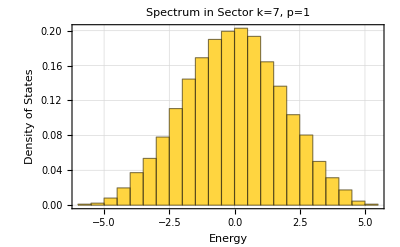

```mathematica
(* 2. Select our target symmetry sector *)
Nspins=L+2;
targetK = Nspins/2; (* Half-filling: 5 up-spins *)
targetP = 1;          (* Even Parity *)

(* 3. Build Projector and reduce the Hamiltonian *)
V = BuildSectorProjector[L, targetK, targetP];
Print["Full Hilbert Space Dimension: ", 2^Nspins];
Print["Target Sector Dimension: ", Last[Dimensions[V]]];

(* H_sector = V^T . H . V  (Projects H into the symmetric sub-basis) *)
HSector = Transpose[V] . HT . V;

(* 4. Diagonalize the sector and compute the r-statistic *)
sectorEnergies = Eigenvalues[HSector];
rStat = LevelSpacingRatio[sectorEnergies];

Print["\nMean Level Spacing Ratio <r> for (k=", targetK, ", P=", targetP, "): ", rStat];

(* INTERPRETATION GUIDE:
   <r> ~ 0.386 indicates Integrability (Poisson statistics)
   <r> ~ 0.530 indicates Quantum Chaos (GOE / Wigner-Dyson statistics)
*)

(* Plot the density of states to see the spectrum *)
Histogram[sectorEnergies, 30, "PDF", 
  PlotTheme -> "Detailed", 
  FrameLabel -> {"Energy", "Density of States"}, 
  PlotLabel -> Row[{"Spectrum in Sector k=", targetK, ", p=", targetP}]
]
```

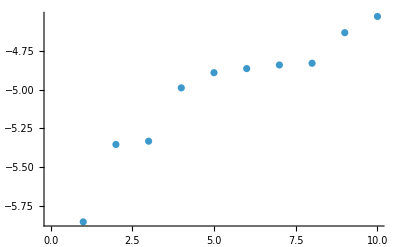

```mathematica
ListPlot[Sort[sectorEnergies][[1;;10]]]
```

```mathematica
data=Unfold[Sort[sectorEnergies]];
```

```mathematica
data//Dimensions
```

{5}

```mathematica
Sort[sectorEnergies][[1]]
Sort[sectorEnergies][[2]]
```

-5.85355

-5.35403

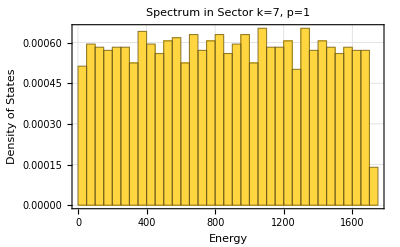

```mathematica
Histogram[data[[1]], 30, "PDF", 
  PlotTheme -> "Detailed", 
  FrameLabel -> {"Energy", "Density of States"}, 
  PlotLabel -> Row[{"Spectrum in Sector k=", targetK, ", p=", targetP}]
]
```

```mathematica
(* ================================================================ *)
(* SPECTRAL ANALYSIS WORKFLOW (ALL SECTORS)                         *)
(* ================================================================ *)
(* Build full Hamiltonian *)
(* Using your exact variables - ensure BuildFullHamiltonian is loaded *)
{Δa, Δb, λa, λb} = {1., 1., 1., 1.};
{Jxy, Jz, w, ed, d} = {1.,2., 0., 0., L};
```

```mathematica
HT = Chop[BuildFullHamiltonian[HAlocal, Ha, HBlocal, couplingA, couplingB, L]];
(* 2. Initialize list to store results *)
spectralResults = {};
```

```mathematica
(* 3. Loop over all Magnetization (k) and Parity (p) sectors *)
Print["Starting spectral analysis across all sectors..."];
AbsoluteTiming[
  Do[
    Do[
      Module[{V, dimSector, HSector, sectorEnergies, rStat},
        (* Build Projector for this specific k and p *)
        V = BuildSectorProjector[L, k, p];
        dimSector = Last[Dimensions[V]];
        
        (* Only compute statistics if the sector has at least 3 levels *)
        If[dimSector >= 3,
          (* Project H into the sub-basis and explicitly make it Normal (dense) 
             to prevent the Eigenvalues::arh warning *)
          HSector = Normal[Transpose[V] . HT . V];
          
          (* Diagonalize and compute <r> *)
          sectorEnergies = Eigenvalues[HSector];
          rStat = LevelSpacingRatio[sectorEnergies];
          
          (* Store result *)
          AppendTo[spectralResults, {k, p, dimSector, rStat}];
        ];
      ],
      {p, {1, -1}} (* Parity can be +1 (Symmetric) or -1 (Antisymmetric) *)
    ],
    {k, 0, Nspins} (* Magnetization ranges from 0 to Total Spins *)
  ]
]

(* 4. Format and display the results *)
Print["\n=== FULL SPECTRUM SYMMETRY ANALYSIS ==="];
PrependTo[spectralResults, {"k (Up-spins)", "Parity (p)", "Dimension", "<r> Ratio"}];

Grid[spectralResults, 
  Frame -> All, 
  Background -> {None, {LightBlue, None}}, 
  Alignment -> Center
]
```

Starting spectral analysis across all sectors...

{3.82781,Null}

=== FULL SPECTRUM SYMMETRY ANALYSIS ===

k (Up-spins) | Parity (p) | Dimension | <r> Ratio
1 | 1 | 7 | 0.635497
1 | -1 | 7 | 0.634002
2 | 1 | 49 | 0.526012
2 | -1 | 42 | 0.580544
3 | 1 | 182 | 0.419875
3 | -1 | 182 | 0.455712
4 | 1 | 511 | 0.389567
4 | -1 | 490 | 0.393274
5 | 1 | 1001 | 0.387941
5 | -1 | 1001 | 0.391712
6 | 1 | 1519 | 0.399831
6 | -1 | 1484 | 0.401028
7 | 1 | 1716 | 0.414594
7 | -1 | 1716 | 0.423376
8 | 1 | 1519 | 0.400211
8 | -1 | 1484 | 0.408989
9 | 1 | 1001 | 0.40411
9 | -1 | 1001 | 0.392625
10 | 1 | 511 | 0.425757
10 | -1 | 490 | 0.413306
11 | 1 | 182 | 0.439252
11 | -1 | 182 | 0.440557
12 | 1 | 49 | 0.470447
12 | -1 | 42 | 0.473751
13 | 1 | 7 | 0.671418
13 | -1 | 7 | 0.690028

```mathematica
(* ================================================================ *)
(* MODULE: Raw Level Spacing Ratios & Analytical P(r)               *)
(* ================================================================ *)
ClearAll[GetLevelSpacingRatios, PPoisson, PGOE];
GetLevelSpacingRatios[energies_List] := Module[{spacings},
  spacings = Differences[Sort[energies]];
  spacings = Select[spacings, # > 1.*^-10 &]; (* Remove degeneracies *)
  If[Length[spacings] < 2, Return[{}]];
    MapThread[Min[#1, #2] / Max[#1, #2] &, {Drop[spacings, -1], Rest[spacings]}]
];
(* Analytical distributions from Atas et al. (2013) *)
PPoisson[r_] := 2 / (1 + r)^2;
PGOE[r_] := (27 / 8) * (r + r^2) / (1 + r + r^2)^(5/2);
```

```mathematica
(* ================================================================ *)
(* SPECTRAL ANALYSIS: Saving Distributions                          *)
(* ================================================================ *)
L = 12;  (* Assuming L=14 based on your output max dimension 6470 *)
SzTot = BuildTotalSz[L];
Pmat = BuildParity[L];
Nspins = L + 2;
{Δa, Δb, λa, λb} = {1., 1., 1., 1.};
{Jxy, Jz, w, ed, d} = {-1., 2., 0., 0., L};
HT = Chop[BuildFullHamiltonian[HAlocal, Ha, HBlocal, couplingA, couplingB, L]];

(* Store the raw r-lists in an Association keyed by {k, p} *)
distributionsData = <||>;
Print["Extracting distributions across all sectors..."];
AbsoluteTiming[
  Do[
    Do[
      Module[{V, dimSector, HSector, sectorEnergies, rList,data},
        V = BuildSectorProjector[L, k, p];
        dimSector = Last[Dimensions[V]];
        
        If[dimSector >= 10, (* Only store if we have enough states to plot *)
          HSector = Normal[Transpose[V] . HT . V];
          sectorEnergies = Eigenvalues[HSector];
data=Unfold[Sort[sectorEnergies]];
          rList = GetLevelSpacingRatios[data[[1]]];
                    (* Save the list to our dictionary *)
          distributionsData[{k, p}] = rList;
        ];
      ],
      {p, {1, -1}}
    ],
    {k, 0, Nspins}
  ]
]
```

Extracting distributions across all sectors...

{4.98753,Null}

```mathematica
(* ================================================================ *)
(* INTERACTIVE VIEWER: Empirical P(r) vs Analytical                 *)
(* ================================================================ *)

(* Get the list of available sectors that were saved *)
availableSectors = Keys[distributionsData];

Manipulate[
  Module[{rList, meanR, dimSector},
    rList = distributionsData[sector];
    dimSector = Length[rList] + 2;
    meanR = Mean[rList];
    
    Show[
      (* Empirical Histogram *)
      Histogram[rList, {0.05}, "PDF",
        ChartElementFunction->"FadingRectangle",
        ChartStyle -> Directive[EdgeForm[White], Gray]
      ],
      
      (* Analytical Curves *)
      Plot[{PPoisson[r], PGOE[r]}, {r, 0, 1},
        PlotStyle -> {
          Directive[Thick, Dashed, Black], 
          Directive[Thick, Red]
        },
        PlotLegends -> Placed[{"Poisson (Integrable)", "GOE (Chaotic)"}, {0.8, 0.8}]
      ],
      
      (* Plot Formatting *)
      PlotRange -> {{0, 1}, {0, 2.5}},
      Frame -> True,
      FrameLabel -> {"Level Spacing Ratio, r", "P(r)"},
      LabelStyle -> Directive[Black, 14],
      PlotLabel -> Style[
        Row[{"Sector k=", sector[[1]], ", p=", sector[[2]], 
             "  |  Dim: ", dimSector, 
             "  |  <r> = ", Round[meanR, 0.001]}], 
        16, Bold
      ],
      ImageSize -> 600
    ]
  ],
  {{sector, availableSectors[[Round[Length[availableSectors]/2]]], "Select Sector {k, p}:"}, 
   availableSectors, ControlType -> PopupMenu}
]
```

Mean::rectt: Rectangular array expected at position 1 in Mean[<|r→{0.120033,0.0790366,0.141235,0.619304,0.579372,0.208573,0.761701,0.536207,0.694726,0.112594,0.0186452,0.276328,0.0115127,0.0139497,0.141771,0.626548,«1338»,0.436726,0.857217,0.16772,0.0393269,0.977558,0.59788,0.187589,0.505961,0.144559,0.850736,0.238404,0.292284,0.5997,0.00844722,0.0259594,0.2689},s→{«1»}|>].

## Unfolding

```mathematica
(* ================================================================ *)
(* MODULE: Normalized Spacings & Analytical P(s)                    *)
(* ================================================================ *)
ClearAll[GetNormalizedSpacings, PPoissonS, PGOES];
GetNormalizedSpacings[unfoldedEnergies_List] := Module[{spacings},
  spacings = Differences[Sort[unfoldedEnergies]];
  spacings = Select[spacings, # > 1.*^-10 &]; (* Remove degeneracies *)
  If[Length[spacings] < 1, Return[{}]];
    (* Normalize so the mean spacing is exactly 1 *)
  spacings / Mean[spacings]
];
(* Analytical distributions for P(s) *)
PPoissonS[s_] := Exp[-s];
PGOES[s_] := (Pi / 2) * s * Exp[-(Pi / 4) * s^2];
```

```mathematica
(* ================================================================ *)
(* SPECTRAL ANALYSIS: Saving Distributions P(r) and P(s)            *)
(* ================================================================ *)
L = 12; 
Nspins = L + 2;
{Δa, Δb, λa, λb} = {1., 1., 1., 1.};
{Jxy, Jz, w, ed, d} = {-1., 2., 0., 0., L};

HT = Chop[BuildFullHamiltonian[HAlocal, Ha, HBlocal, couplingA, couplingB, L]];

distributionsData = <||>;
Print["Extracting r and s distributions across all sectors..."];

AbsoluteTiming[
  Do[
    Do[
      Module[{V, dimSector, HSector, sectorEnergies, rList, sList, data, unfoldedLevels},
        V = BuildSectorProjector[L, k, p];
        dimSector = Last[Dimensions[V]];
        
        If[dimSector >= 10,
          HSector = Normal[Transpose[V] . HT . V];
          sectorEnergies = Eigenvalues[HSector];
          
          (* Unfold the spectrum *)
          data = Unfold[Sort[sectorEnergies]];
          unfoldedLevels = data[[1]];
          
          (* Extract both metrics *)
          rList = GetLevelSpacingRatios[unfoldedLevels];
          sList = GetNormalizedSpacings[unfoldedLevels];
          
          (* Save as a nested Association *)
          distributionsData[{k, p}] = <|"r" -> rList, "s" -> sList|>;
        ];
      ],
      {p, {1, -1}}
    ],
    {k, 0, Nspins}
  ]
]
```

Extracting r and s distributions across all sectors...

{4.4748,Null}

```mathematica
(* ================================================================ *)
(* SPECTRAL ANALYSIS: Saving Distributions with Border Trimming     *)
(* ================================================================ *)
L = 12; 
Nspins = L + 2;
{Δa, Δb, λa, λb} = {1., 1., 1., 1.};
{Jxy, Jz, w, ed, d} = {-1., 3., 0., 0., L};
HT = Chop[BuildFullHamiltonian[HAlocal, Ha, HBlocal, couplingA, couplingB, L]];
distributionsData = <||>;
Print["Extracting trimmed r and s distributions across all sectors..."];
```

Extracting trimmed r and s distributions across all sectors...

```mathematica
(* Set the fraction to discard from EACH border (e.g., 0.05 = 5% from left, 5% from right) *)
trimFraction = 0.1; 

AbsoluteTiming[
  Do[
    Do[
      Module[{V, dimSector, HSector, sectorEnergies, data, unfoldedLevels, 
              nTrim, trimmedLevels, rList, sList},
        V = BuildSectorProjector[L, k, p];
        dimSector = Last[Dimensions[V]];
        
        If[dimSector >= 10,
          HSector = Normal[Transpose[V] . HT . V];
          sectorEnergies = Eigenvalues[HSector];
          
          (* 1. Unfold the sorted spectrum *)
          data = Unfold[Sort[sectorEnergies]];
          unfoldedLevels = data[[1]];
          
          (* 2. Calculate how many states to drop from each side *)
          nTrim = Round[Length[unfoldedLevels] * trimFraction];
          
          (* 3. Slice the list using Span (;;), dropping the first and last nTrim elements *)
          If[Length[unfoldedLevels] - 2 * nTrim >= 10,
            trimmedLevels = unfoldedLevels[[1 + nTrim ;; -1 - nTrim]];
            
            (* 4. Extract metrics from the bulk of the spectrum *)
            rList = GetLevelSpacingRatios[trimmedLevels];
            sList = GetNormalizedSpacings[trimmedLevels];
            
            (* Save to dictionary *)
            distributionsData[{k, p}] = <|"r" -> rList, "s" -> sList|>;
          ];
        ];
      ],
      {p, {1, -1}}
    ],
    {k, 0, Nspins}
  ]
]
```

{4.89569,Null}

```mathematica
(* ================================================================ *)
(* INTERACTIVE VIEWER: Balanced Side-by-Side P(r) & P(s) Plots      *)
(* ================================================================ *)
availableSectors = Keys[distributionsData];

Manipulate[
  Module[{rList, sList, meanR, dimSector, plotR, plotS, panelSize},
    rList = distributionsData[sector]["r"];
    sList = distributionsData[sector]["s"];
    dimSector = Length[rList] + 2;
    meanR = Mean[rList];
    
    (* Define a rigid size for both plot panels {Width, Height} *)
    panelSize = {420, 320};
    
    (* 1. Build the P(r) Plot *)
    plotR = Show[
      Histogram[rList, {0.05}, "PDF",
        ChartElementFunction -> "GlassRectangle",
        ChartStyle -> Directive[EdgeForm[White], LightBlue]
      ],
      Plot[{PPoisson[r], PGOE[r]}, {r, 0, 1},
        PlotStyle -> {Directive[Thick, Dashed, Black], Directive[Thick, Red]}
      ],
      PlotRange -> {{0, 1}, {0, 2.5}},
      Frame -> True, 
      FrameLabel -> {"r", "P(r)"},
      LabelStyle -> Directive[Black, 12],
      PlotLabel -> Style["Level Spacing Ratio P(r)", 14, Bold],
      ImageSize -> panelSize,
      AspectRatio -> Full
    ];
    
    (* 2. Build the P(s) Plot *)
    plotS = Show[
      Histogram[sList, {0.15}, "PDF",
        ChartElementFunction -> "GlassRectangle",
        ChartStyle -> Directive[EdgeForm[White], LightGreen]
      ],
      Plot[{PPoissonS[s], PGOES[s]}, {s, 0, 4},
        PlotStyle -> {Directive[Thick, Dashed, Black], Directive[Thick, Red]},
        PlotLegends -> Placed[{"Poisson", "GOE"}, After]
      ],
      PlotRange -> {{0, 4}, {0, 1.2}},
      Frame -> True, 
      FrameLabel -> {"s", "P(s)"},
      LabelStyle -> Directive[Black, 12],
      PlotLabel -> Style["Nearest-Neighbor Spacing P(s)", 14, Bold],
      ImageSize -> panelSize,
      AspectRatio -> Full
    ];
    
    (* 3. Combine them side-by-side using Row to preserve dimensions *)
    Column[{
      Style[Row[{"Sector k=", sector[[1]], ", p=", sector[[2]], 
                 "  |  Dim: ", dimSector, 
                 "  |  <r> = ", Round[meanR, 0.001]}], 16, Bold],
      Spacer[10],
      Row[{plotR, Spacer[20], plotS}]
    }, Alignment -> Center]
  ],
  {{sector, availableSectors[[Round[Length[availableSectors]/2]]], "Select Sector {k, p}:"}, 
   availableSectors, ControlType -> PopupMenu}
]
```

```mathematica
(* ================================================================ *)
(* INTERACTIVE VIEWER: Balanced Side-by-Side P(r) & P(s) Plots      *)
(* ================================================================ *)
availableSectors = Keys[distributionsData];

Manipulate[
  Module[{rList, sList, meanR, dimSector, plotR, plotS, panelSize},
    rList = distributionsData[sector]["r"];
    sList = distributionsData[sector]["s"];
    dimSector = Length[rList] + 2;
    meanR = Mean[rList];
    
    (* Define a rigid size for both plot panels {Width, Height} *)
    panelSize = {420, 320};
    
    (* 1. Build the P(r) Plot *)
    plotR = Show[
      Histogram[rList, {0.05}, "PDF",
        ChartElementFunction -> "GlassRectangle",
        ChartStyle -> Directive[EdgeForm[White], LightBlue]
      ],
      Plot[{PPoisson[r], PGOE[r]}, {r, 0, 1},
        PlotStyle -> {Directive[Thick, Dashed, Black], Directive[Thick, Red]}
      ],
      PlotRange -> {{0, 1}, {0, 2.5}},
      Frame -> True, 
      FrameLabel -> {"r", "P(r)"},
      LabelStyle -> Directive[Black, 12],
      PlotLabel -> Style["Level Spacing Ratio P(r)", 14, Bold],
      ImageSize -> panelSize,
      AspectRatio -> Full
    ];
    
    (* 2. Build the P(s) Plot *)
    plotS = Show[
      Histogram[sList, {0.15}, "PDF",
        ChartElementFunction -> "GlassRectangle",
        ChartStyle -> Directive[EdgeForm[White], LightGreen]
      ],
      Plot[{PPoissonS[s], PGOES[s]}, {s, 0, 4},
        PlotStyle -> {Directive[Thick, Dashed, Black], Directive[Thick, Red]},
        PlotLegends -> Placed[{"Poisson", "GOE"}, After]
      ],
      PlotRange -> {{0, 4}, {0, 1.2}},
      Frame -> True, 
      FrameLabel -> {"s", "P(s)"},
      LabelStyle -> Directive[Black, 12],
      PlotLabel -> Style["Nearest-Neighbor Spacing P(s)", 14, Bold],
      ImageSize -> panelSize,
      AspectRatio -> Full
    ];
    
    (* 3. Combine them side-by-side using Row to preserve dimensions *)
    Column[{
      Style[Row[{"Sector k=", sector[[1]], ", p=", sector[[2]], 
                 "  |  Dim: ", dimSector, 
                 "  |  <r> = ", Round[meanR, 0.001]}], 16, Bold],
      Spacer[10],
      Row[{plotR, Spacer[20], plotS}]
    }, Alignment -> Center]
  ],
  {{sector, availableSectors[[Round[Length[availableSectors]/2]]], "Select Sector {k, p}:"}, 
   availableSectors, ControlType -> PopupMenu}
]
```

## SFF

```mathematica
(* ============================================================*)(*1. ENSEMBLE GENERATION (XXZ MODEL)*)(* ============================================================*)L=12;
targetK=7;
targetP=1;
Nspins=L+2;
{Δa,Δb,λa,λb}={1.,1.,1.,1.};
baseJz=0.2;
{Jxy,w,ed,d}={-1.,0.,0,7}; (*ed=1.5 for Chaos*)

nRealizations=100;
trimFraction=0.05;

V=BuildSectorProjector[L,targetK,targetP];
HTemplate[Jz_]:=Chop[BuildFullHamiltonian[HAlocal,XXZwLocalDefectHamiltonian[Jxy,Jz,w,ed,L,d],HBlocal,couplingA,couplingB,L]];

unfoldedEnsemble={};
Print["Generating ensemble of ",nRealizations," spectra..."];

AbsoluteTiming[Do[Module[{currentJz,HT,HSector,sectorEnergies,data,unfoldedLevels,nTrim,trimmedLevels},currentJz=baseJz*(1.+RandomReal[{-0.005,0.005}]);
HT=HTemplate[currentJz];
HSector=Normal[Transpose[V].HT.V];
sectorEnergies=Sort[Eigenvalues[HSector]];
data=Unfold[sectorEnergies];
unfoldedLevels=data[[1]];
nTrim=Round[Length[unfoldedLevels]*trimFraction];
If[Length[unfoldedLevels]-2*nTrim>10,trimmedLevels=unfoldedLevels[[1+nTrim;;-1-nTrim]];
AppendTo[unfoldedEnsemble,trimmedLevels];];],{n,1,nRealizations}]]
```

Generating ensemble of 100 spectra...

{57.7243,Null}

```mathematica
(* ============================================================*)(*2. SFF IN HEISENBERG UNITS& SMOOTHING*)(* ============================================================*)Clear[SmoothSFF,EnsembleKFromEnergies];
SmoothSFF[kVec_List,tauVec_List,sigmaTau_?NumericQ]:=GaussianFilter[kVec,sigmaTau/(tauVec[[2]]-tauVec[[1]])];
EnsembleKFromEnergies[ensEnergies_List,tauMax_?NumericQ,nPts_Integer]:=Module[{tauList,allK},tauList=N[Range[1,nPts] (tauMax/nPts)];
allK=With[{en=ensEnergies,tL=tauList},ParallelTable[Module[{energies=en[[i]],tauFactors},(*For unfolded energies,phase is exactly 2 π τ E*)tauFactors=tL*2*Pi;
Abs[Exp[-I*Outer[Times,tauFactors,energies]].ConstantArray[1.,Length[energies]]]^2/Length[energies]],{i,Length[ensEnergies]},Method->"CoarsestGrained"]];
<|"Tau"->tauList,"AllK"->allK,"MeanK"->Mean[allK]|>];

(*Parameters for computation*)
tauMaxSFF=3.0;
nPtsSFF=10000; (*Reduced slightly from 10k so it computes in seconds*)
sigmaSmSFF=0.05; (*Adjusted smoothing width*)

Print["Computing SFF over τ..."];
AbsoluteTiming[sffData=EnsembleKFromEnergies[unfoldedEnsemble,tauMaxSFF,nPtsSFF];]

tauGrid=sffData["Tau"];
kAllSm=Map[SmoothSFF[#,tauGrid,sigmaSmSFF]&,sffData["AllK"]];
kMeanSm=Mean[kAllSm];

(*GOE analytical SFF (Mathematically identical to your COE form)*)
kGOEAn=Table[If[t<=1.,2 t-t Log[1+2 t],2-t Log[(2 t+1)/(2 t-1)]],{t,tauGrid}];
```

Computing SFF over τ...

{33.1377,Null}

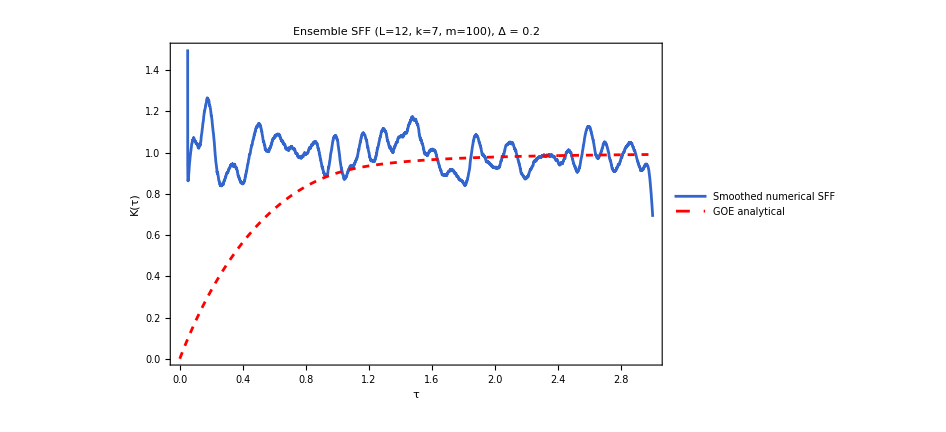

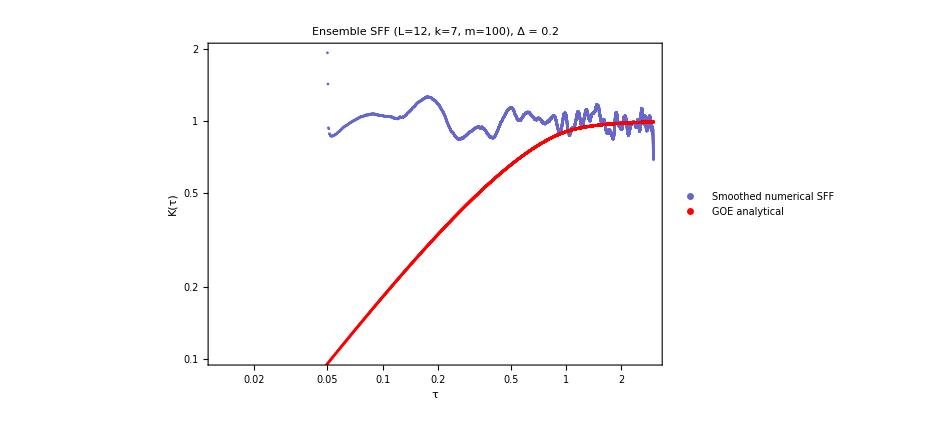

```mathematica
(* ============================================================*)(*3. PLOTTING (Linear and Log-Log)*)(* ============================================================*)plotEnsemble=ListLinePlot[{Transpose[{tauGrid,kMeanSm}],Transpose[{tauGrid,kGOEAn}]},PlotStyle->{Directive[Thick,RGBColor[0.2,0.4,0.8]],Directive[Thick,Dashed,Red]},PlotLegends->{"Smoothed numerical SFF","GOE analytical"},Frame->True,FrameLabel->{"τ","K(τ)"},PlotLabel->"Ensemble SFF (L="<>ToString[L]<>", k="<>ToString[targetK]<>", m="<>ToString[Length[unfoldedEnsemble]]<>"), Δ = "<>ToString[baseJz],ImageSize->700,LabelStyle->Directive[Black,20],PlotRange->{{0,3},{0,1.5}}]

plotLogLog=ListLogLogPlot[{Transpose[{tauGrid,kMeanSm}],Transpose[{tauGrid,kGOEAn}]},PlotStyle->{Directive[Thick,RGBColor[0.4,0.4,0.8]],Directive[Thick,Dashed,Red]},PlotLegends->{"Smoothed numerical SFF","GOE analytical"},Frame->True,FrameLabel->{"τ","K(τ)"},PlotLabel->"Ensemble SFF (L="<>ToString[L]<>", k="<>ToString[targetK]<>", m="<>ToString[Length[unfoldedEnsemble]]<>"), Δ = "<>ToString[baseJz],ImageSize->700,LabelStyle->Directive[Black,20],PlotRange->{{0.0125,3},{0.1,2}}]
```

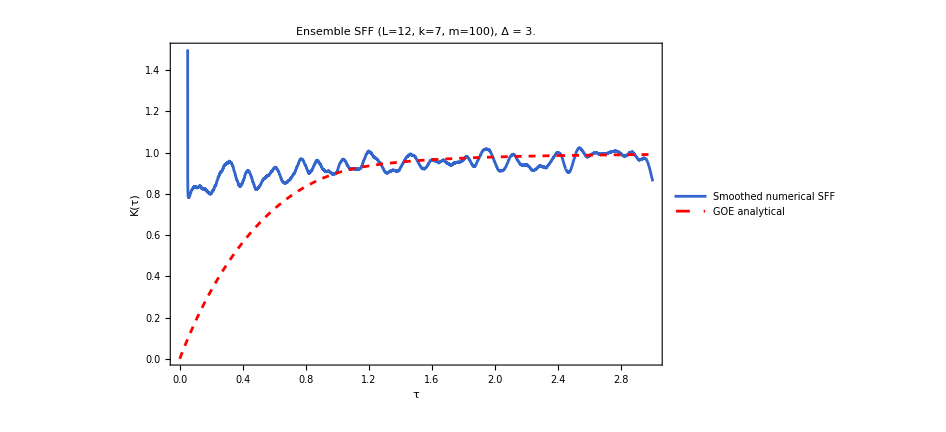

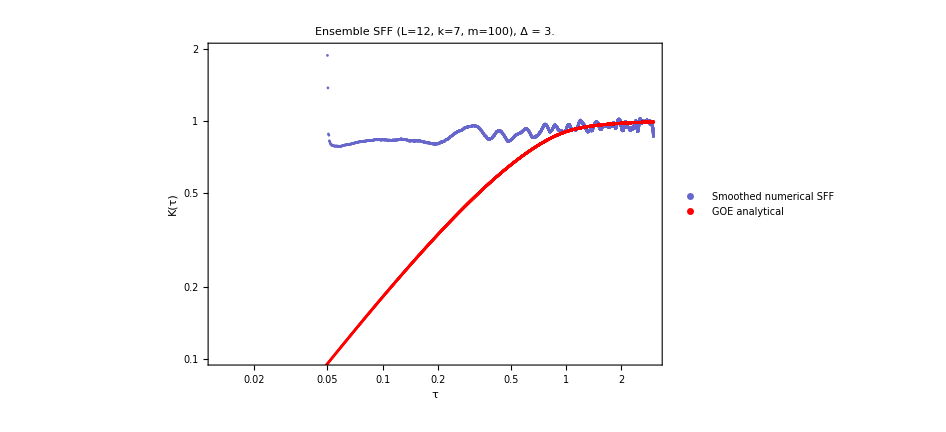

```mathematica
(* ============================================================*)(*3. PLOTTING (Linear and Log-Log)*)(* ============================================================*)plotEnsemble=ListLinePlot[{Transpose[{tauGrid,kMeanSm}],Transpose[{tauGrid,kGOEAn}]},PlotStyle->{Directive[Thick,RGBColor[0.2,0.4,0.8]],Directive[Thick,Dashed,Red]},PlotLegends->{"Smoothed numerical SFF","GOE analytical"},Frame->True,FrameLabel->{"τ","K(τ)"},PlotLabel->"Ensemble SFF (L="<>ToString[L]<>", k="<>ToString[targetK]<>", m="<>ToString[Length[unfoldedEnsemble]]<>"), Δ = "<>ToString[baseJz],ImageSize->700,LabelStyle->Directive[Black,20],PlotRange->{{0,3},{0,1.5}}]

plotLogLog=ListLogLogPlot[{Transpose[{tauGrid,kMeanSm}],Transpose[{tauGrid,kGOEAn}]},PlotStyle->{Directive[Thick,RGBColor[0.4,0.4,0.8]],Directive[Thick,Dashed,Red]},PlotLegends->{"Smoothed numerical SFF","GOE analytical"},Frame->True,FrameLabel->{"τ","K(τ)"},PlotLabel->"Ensemble SFF (L="<>ToString[L]<>", k="<>ToString[targetK]<>", m="<>ToString[Length[unfoldedEnsemble]]<>"), Δ = "<>ToString[baseJz],ImageSize->700,LabelStyle->Directive[Black,20],PlotRange->{{0.0125,3},{0.1,2}}]
```